```mathematica
ListSigmaOfΣn[Σn_]:=Join[Σn/@domain[Σn],ListComplement[ListSigmaAll,Σn/@domain[Σn]]]
```

```mathematica
ListSigmaOfΣn[ΣnXISO]
ListSigmaOfΣn[ΣnCUBE]
```

{TRIV,MONO,ORTH,TET,XISO,ISO,TRIG,CUBE}

{TRIV,MONO,ORTH,TET,CUBE,ISO,XISO,TRIG}

```mathematica
SigmaPairsMatrix[Σn_,dim_]:=Table[{Take[ListSigmaOfΣn[Σn],dim][[j]],Take[ListSigmaOfΣn[Σn],dim][[k]]},{j,dim},{k,dim}];
MatrixForm[SigmaPairsMatrix[ΣnCUBE,6]]
```

((TRIV
TRIV) | (TRIV
MONO) | (TRIV
ORTH) | (TRIV
TET) | (TRIV
CUBE) | (TRIV
ISO)
(MONO
TRIV) | (MONO
MONO) | (MONO
ORTH) | (MONO
TET) | (MONO
CUBE) | (MONO
ISO)
(ORTH
TRIV) | (ORTH
MONO) | (ORTH
ORTH) | (ORTH
TET) | (ORTH
CUBE) | (ORTH
ISO)
(TET
TRIV) | (TET
MONO) | (TET
ORTH) | (TET
TET) | (TET
CUBE) | (TET
ISO)
(CUBE
TRIV) | (CUBE
MONO) | (CUBE
ORTH) | (CUBE
TET) | (CUBE
CUBE) | (CUBE
ISO)
(ISO
TRIV) | (ISO
MONO) | (ISO
ORTH) | (ISO
TET) | (ISO
CUBE) | (ISO
ISO))

#### Here is how the Map function works .

```mathematica
MatrixForm[Map[#[[1]]+#[[2]]&,SigmaPairsMatrix[ΣnCUBE,6],{2}]]
```

(2 TRIV | MONO+TRIV | ORTH+TRIV | TET+TRIV | CUBE+TRIV | ISO+TRIV
MONO+TRIV | 2 MONO | MONO+ORTH | MONO+TET | CUBE+MONO | ISO+MONO
ORTH+TRIV | MONO+ORTH | 2 ORTH | ORTH+TET | CUBE+ORTH | ISO+ORTH
TET+TRIV | MONO+TET | ORTH+TET | 2 TET | CUBE+TET | ISO+TET
CUBE+TRIV | CUBE+MONO | CUBE+ORTH | CUBE+TET | 2 CUBE | CUBE+ISO
ISO+TRIV | ISO+MONO | ISO+ORTH | ISO+TET | CUBE+ISO | 2 ISO)

```mathematica
InternodalAngles[Tmat_,Σn_,nm_,dim_]:=Map[Round[AngleMatrix[SmatOfΣ[#[[1]],Tmat,Σn,nm],SmatOfΣ[#[[2]],Tmat,Σn,nm]]/Degree,.01]&,SigmaPairsMatrix[Σn,dim],{2}];
```

```mathematica
MatrixNote[Tmat]
MatrixForm[InternodalAngles[Tmat,ΣnCUBE,nm2,6]]
MatrixForm[InternodalAngles[Tmat,ΣnCUBE,nm2,8]]
```

Tmat is TmatBrownNew

(0. | 3.77 | 6.42 | 7.86 | 21.12 | 26.04
3.77 | 0. | 5.22 | 6.97 | 20.95 | 25.78
6.42 | 5.22 | 0. | 4.82 | 20.36 | 25.29
7.86 | 6.97 | 4.82 | 0. | 19.76 | 24.9
21.12 | 20.95 | 20.36 | 19.76 | 0. | 15.59
26.04 | 25.78 | 25.29 | 24.9 | 15.59 | 0.)

(0. | 3.77 | 6.42 | 7.86 | 21.12 | 26.04 | 18.62 | 16.23
3.77 | 0. | 5.22 | 6.97 | 20.95 | 25.78 | 19.02 | 16.47
6.42 | 5.22 | 0. | 4.82 | 20.36 | 25.29 | 18.31 | 18.82
7.86 | 6.97 | 4.82 | 0. | 19.76 | 24.9 | 17.92 | 19.79
21.12 | 20.95 | 20.36 | 19.76 | 0. | 15.59 | 13.21 | 22.4
26.04 | 25.78 | 25.29 | 24.9 | 15.59 | 0. | 18.54 | 20.64
18.62 | 19.02 | 18.31 | 17.92 | 13.21 | 18.54 | 0. | 20.68
16.23 | 16.47 | 18.82 | 19.79 | 22.4 | 20.64 | 20.68 | 0.)

```mathematica
ff[i_,j_,Tmat_,Σn_,nm_,dim_]:=InternodalAngles[Tmat,Σn,nm,dim][[i,j]];
```

```mathematica
nm=nm3;
MatrixNote[Tmat]
ff[4,5,Tmat,ΣnXISO,nm,6]
```

Tmat is TmatBrownNew

17.69

```mathematica
MaxForScaling:=InternodalAngles[Tmat,Σn,nm2,6][[1,6]];
```

```mathematica
MaxForScaling
```

26.04

```mathematica
PreCheckerboard[Tmat_,Σn_,nm_,dim_,MaxForScaling_]:=Graphics[Table[{FaceForm[ColorData["TemperatureMap"][ff[i,j,Tmat,Σn,nm,dim]/MaxForScaling]],Cuboid[{i-.5,-j-.5},{i+.5,-j+.5}]},{i,dim},{j,dim}]]
```

```mathematica
Checkerboard[Tmat_,Σn_,nm_,dim_,MaxForScaling_]:=Show[{Graphics[{
Text[#,{Position[Take[ListSigmaOfΣn[Σn],dim],#][[1,1]],0}]&/@Take[ListSigmaOfΣn[Σn],dim],
Text[#,{-.2,-Position[Take[ListSigmaOfΣn[Σn],dim],#][[1,1]]}]&/@Take[ListSigmaOfΣn[Σn],dim]}],PreCheckerboard[Tmat,Σn,nm,dim,MaxForScaling]},ImageSize->320 dim/6];
```

```mathematica
rrow[i_,Tmat_,Σn_,nm_,dim_]:=Join[{Take[ListSigmaOfΣn[Σn],dim][[i]]},InternodalAngles[Tmat,Σn,nm,dim][[i]]];
rrow[0,Tmat_,Σn_,nm_,dim_]:=Join[{""},Take[ListSigmaOfΣn[Σn],dim]];
```

```mathematica
Σn=ΣnCUBE;dim=8;
rrow[0,Tmat,Σn,nm2,dim]
rrow[3,Tmat,Σn,nm2,dim]
```

{,TRIV,MONO,ORTH,TET,CUBE,ISO,XISO,TRIG}

{ORTH,6.42,5.22,0.,4.82,20.36,25.29,18.31,18.82}

#### Examples

Tmat is TmatBrownNew

Node mode nm4: P(T,𝒱_Σ(U))

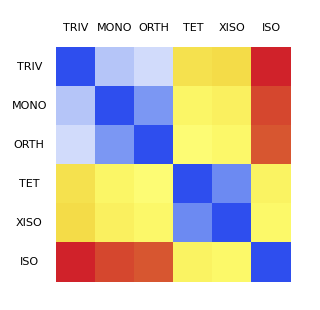

( | TRIV | MONO | ORTH | TET | XISO | ISO
TRIV | 0. | 7.34 | 8.69 | 19.17 | 19.55 | 26.04
MONO | 7.34 | 0. | 4.67 | 17.75 | 18.17 | 25.05
ORTH | 8.69 | 4.67 | 0. | 17.15 | 17.58 | 24.64
TET | 19.17 | 17.75 | 17.15 | 0. | 3.92 | 17.97
XISO | 19.55 | 18.17 | 17.58 | 3.92 | 0. | 17.55
ISO | 26.04 | 25.05 | 24.64 | 17.97 | 17.55 | 0.)

Tmat is TmatBrownNew

Node mode nm2: Closest to Tmat

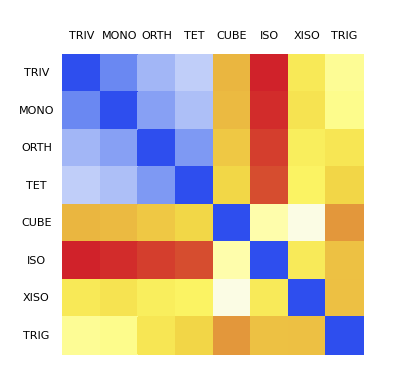

( | TRIV | MONO | ORTH | TET | CUBE | ISO | XISO | TRIG
TRIV | 0. | 3.77 | 6.42 | 7.86 | 21.12 | 26.04 | 18.62 | 16.23
MONO | 3.77 | 0. | 5.22 | 6.97 | 20.95 | 25.78 | 19.02 | 16.47
ORTH | 6.42 | 5.22 | 0. | 4.82 | 20.36 | 25.29 | 18.31 | 18.82
TET | 7.86 | 6.97 | 4.82 | 0. | 19.76 | 24.9 | 17.92 | 19.79
CUBE | 21.12 | 20.95 | 20.36 | 19.76 | 0. | 15.59 | 13.21 | 22.4
ISO | 26.04 | 25.78 | 25.29 | 24.9 | 15.59 | 0. | 18.54 | 20.64
XISO | 18.62 | 19.02 | 18.31 | 17.92 | 13.21 | 18.54 | 0. | 20.68
TRIG | 16.23 | 16.47 | 18.82 | 19.79 | 22.4 | 20.64 | 20.68 | 0.)

Tmat is TmatBrownNew

Node mode nm3: Closest to prior

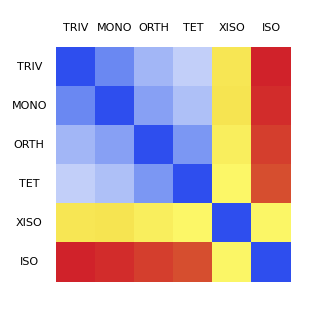

( | TRIV | MONO | ORTH | TET | XISO | ISO
TRIV | 0. | 3.77 | 6.43 | 7.95 | 18.82 | 26.04
MONO | 3.77 | 0. | 5.21 | 7.01 | 18.99 | 25.78
ORTH | 6.43 | 5.21 | 0. | 4.69 | 18.28 | 25.28
TET | 7.95 | 7.01 | 4.69 | 0. | 17.69 | 24.87
XISO | 18.82 | 18.99 | 18.28 | 17.69 | 0. | 17.77
ISO | 26.04 | 25.78 | 25.28 | 24.87 | 17.77 | 0.)

```mathematica
nm=nm4;Σn=ΣnXISO;dim=6;
MatrixNote[Tmat]
TextNodeMode[nm]
Checkerboard[Tmat,Σn,nm,dim,MaxForScaling]
MatrixForm[Table[rrow[i,Tmat,Σn,nm,dim],{i,0,dim}]]
Print[" "];
nm=nm2;Σn=ΣnCUBE;dim=8;
MatrixNote[Tmat]
TextNodeMode[nm]
Checkerboard[Tmat,Σn,nm,dim,MaxForScaling]
MatrixForm[Table[rrow[i,Tmat,Σn,nm,dim],{i,0,dim}]]
Print[" "];
nm=nm3;Σn=ΣnXISO;dim=6;  (* dim must be 6 for nm3 *)
MatrixNote[Tmat]
TextNodeMode[nm]
Checkerboard[Tmat,Σn,nm,dim,MaxForScaling]
MatrixForm[Table[rrow[i,Tmat,Σn,nm,dim],{i,0,dim}]]
Print[" "];
```